## Problem 1

Let 
 denote . Since Mathematica struggles with , we first consider the  case.

```mathematica
X = {{-I*ζ, q[x,t]},{g[x,t],I*ζ}};
```

```mathematica
T = {{-I*ζ^2-I*q[x,t]*g[x,t]/2,q[x,t]*ζ+I*D[q[x,t],x]/2},{g[x,t]*ζ-I*D[g[x,t],x]/2,I*ζ^2+I*q[x,t]*g[x,t]/2}};
```

We enforce the NLS equation by setting  and conjugating, .

```mathematica
enforceNLS1 = {D[q[x,t],t]->I*D[q[x,t],{x,2}]/2-I*q[x,t]^2*g[x,t],D[g[x,t],t]->-I*D[g[x,t],{x,2}]/2+I*g[x,t]^2*q[x,t]};
```

```mathematica
D[X,t]+X.T-D[T,x]-T.X/.enforceNLS1//FullSimplify
```

If the compatibility condition is satisfied, then this should be the zero matrix.

{{0,0},{0,0}}

Now, we consider the  case.

```mathematica
X = {{-I*ζ, q[x,t]},{-g[x,t],I*ζ}};
```

```mathematica
T = {{-I*ζ^2+I*q[x,t]*g[x,t]/2,q[x,t]*ζ+I*D[q[x,t],x]/2},{-g[x,t]*ζ+I*D[g[x,t],x]/2,I*ζ^2-I*q[x,t]*g[x,t]/2}};
```

```mathematica
enforceNLS2= {D[q[x,t],t]->I*D[q[x,t],{x,2}]/2+I*q[x,t]^2*g[x,t],D[g[x,t],t]->-I*D[g[x,t],{x,2}]/2-I*g[x,t]^2*q[x,t]};
```

If the compatibility condition is satisfied, then this should be the zero matrix.

```mathematica
D[X,t]+X.T-D[T,x]-T.X/.enforceNLS2//FullSimplify
```

{{0,0},{0,0}}

## Problem 2

```mathematica
Clear[X,T]
```

```mathematica
X[n_]= {{z,q[n,t]},{g[n,t], 1/z}}
```

{{z,q[n,t]},{g[n,t],1/z}}

```mathematica
T[n_]={{I*q[n,t]*g[n-1,t]-I*(1/z-z)^2/2,I*q[n-1,t]/z-I*z*q[n,t]},{-I*z*g[n-1,t]+I*g[n,t]/z,-I*g[n,t]*q[n-1,t]+I*(1/z-z)^2/2}}
```

{{-1/2 ⅈ (1/z-z)^2+ⅈ g[-1+n,t] q[n,t],(ⅈ q[-1+n,t])/z-ⅈ z q[n,t]},{-ⅈ z g[-1+n,t]+(ⅈ g[n,t])/z,1/2 ⅈ (1/z-z)^2-ⅈ g[n,t] q[-1+n,t]}}

We enforce the semi-discrete equation in the same manner as problem 1, namely by multiplying through by  to get the first equation and conjugating to get a second equation.

```mathematica
enforceDNLS={D[q[n,t],t]->-I*(q[n+1,t]-2*q[n,t]+q[n-1,t]-q[n,t]*g[n,t]*(q[n+1,t]+q[n-1,t])),D[g[n,t],t]->I*(g[n+1,t]-2*g[n,t]+g[n-1,t]-g[n,t]*q[n,t]*(g[n+1,t]+g[n-1,t]))};
```

If the compatibility condition is satisfied, then this should be the zero matrix.

```mathematica
D[X[n],t]+X[n].T[n]-T[n+1].X[n]/.enforceDNLS//FullSimplify
```

{{0,0},{0,0}}

## Problem 3

We first solve for the constants to match our initial condition.

```mathematica
consts = Solve[{Exp[I*k*L]==c3*Exp[-I*Sqrt[k^2+d]*L]+c4*Exp[I*Sqrt[k^2+d]*L],-I*k*Exp[I*k*L]==I*Sqrt[k^2+d]*c3*Exp[-I*Sqrt[k^2+d]*L]-I*Sqrt[k^2+d]*c4*Exp[I*Sqrt[k^2+d]*L]},{c3,c4}]
```

{{c3→(ⅇ^(ⅈ k L+ⅈ √(d+k^2) L) (-k+√(d+k^2)))/(2 √(d+k^2)),c4→(ⅇ^(ⅈ k L-ⅈ √(d+k^2) L) (k+√(d+k^2)))/(2 √(d+k^2))}}

```mathematica
consts2=Solve[{c1*Exp[I*k*L]+c2*Exp[-I*k*L]==c3*Exp[I*Sqrt[k^2+d]*L]+c4*Exp[-I*Sqrt[k^2+d]*L],I*k*c1*Exp[I*k*L]-I*k*c2*Exp[-I*k*L]==I*Sqrt[k^2+d]*c3*Exp[I*Sqrt[k^2+d]*L]-I*Sqrt[k^2+d]*c4*Exp[-I*Sqrt[k^2+d]*L]},{c1,c2}]/.consts//Simplify
```

{{{c1→(d ⅇ^(-2 ⅈ √(d+k^2) L) (-1+ⅇ^(4 ⅈ √(d+k^2) L)))/(4 k √(d+k^2)),c2→1/(4 k √(d+k^2))ⅇ^(-2 ⅈ (-k+√(d+k^2)) L) (d-d ⅇ^(4 ⅈ √(d+k^2) L)+2 k (k-ⅇ^(4 ⅈ √(d+k^2) L) k+(1+ⅇ^(4 ⅈ √(d+k^2) L)) √(d+k^2)))}}}

Now, we define  and  for  and compute  via their Wronskian.

```mathematica
ϕ[x_]:=c1*Exp[I*k*x]+c2*Exp[-I*k*x]/.consts2
```

```mathematica
φ[x_]:=Exp[I*k*x]
```

```mathematica
a[k_]=(ϕ[x]*D[φ[x],x]-D[ϕ[x],x]*φ[x])/(2*I*k)//FullSimplify
```

{{1/2 ⅇ^(2 ⅈ k L) (2 Cos[2 √(d+k^2) L]-(ⅈ (d+2 k^2) Sin[2 √(d+k^2) L])/(k √(d+k^2)))}}

Here, we look at .

```mathematica
aa[κ_]=a[k]/.k->I*κ
```

{{{1/2 ⅇ^(-2 L κ) (2 Cos[2 L √(d-κ^2)]-((d-2 κ^2) Sin[2 L √(d-κ^2)])/(κ √(d-κ^2)))}}}

We use this substitution to help analyze the case where .

```mathematica
aat[κ_]=Simplify[aa[κ]/.√(d-κ^2)->I*m]
```

{{{1/2 ⅇ^(-2 L κ) (2 Cosh[2 L m]-(ⅈ (d-2 κ^2) Sinh[2 L m])/(κ √(d-κ^2)))}}}

Now, we substitute in our scaling.

```mathematica
aaa[s_]=Simplify[aa[κ]/.{√(d-κ^2)->s/(2L),κ->Sqrt[d-(s/(2L))^2]},Assumptions->{L>0,κ>=0,s>0,κ^2>d,d-(s/L)^2>0}]
```

{{{(ⅇ^(-√(4 d L^2-s^2)) (s √(4 d L^2-s^2) Cos[s]+(2 d L^2-s^2) Sin[s]))/(s √(4 d L^2-s^2))}}}

Setting , it should suffice to set this function to zero.

```mathematica
aaaa[s_,p_]=Cot[s]-s*(s^2-p)/(s*Sqrt[2p-s^2])
```

-(-p+s^2)/(√(2 p-s^2))+Cot[s]

We plot both terms of our expression to find intersection points. From this, we conjecture that the number of zeros is given by .

```mathematica
Manipulate[Plot[{Cot[s],(s^2-p)/(s*Sqrt[2p-s^2])},{s,0,20},PlotRange->{-10,10},PlotPoints->200],{p,0.1,150}]
```

If our conjecture is correct, we should expect one zero here.

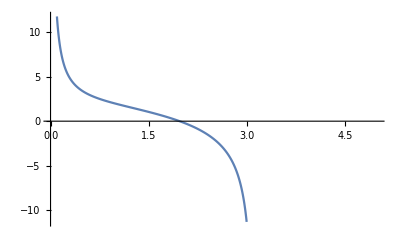

```mathematica
Plot[aaaa[s,Pi^2/2],{s,0,5},PlotPoints->1000]
```

Taking a small positive perturbation, we should expect to see two zeros.

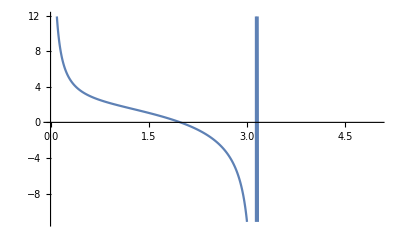

```mathematica
Plot[aaaa[s,Pi^2/2+0.1],{s,0,5},PlotPoints->1000]
```

Similarly, we should expect two zeros here.

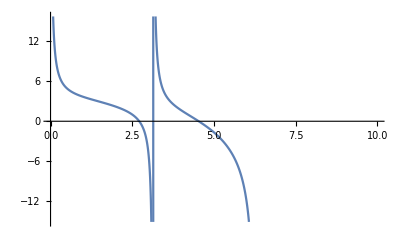

```mathematica
Plot[aaaa[s,2*Pi^2],{s,0,10},PlotPoints->1000]
```

```mathematica
Ceiling[Sqrt[2*60]/Pi]
```

4

This tells us to expect four zeros.

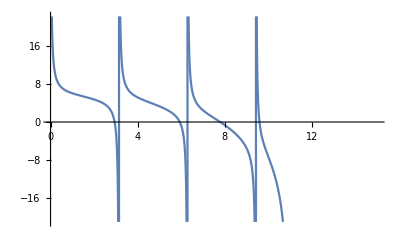

```mathematica
Plot[aaaa[s,60],{s,0,15},PlotPoints->1000]
```

Here, we compute the limit with the desired substitution.

```mathematica
Limit[ a[k]/.d->α/(2L),L->0]
```

{{{1-(ⅈ α)/(2 k)}}}

## Problem 6

```mathematica
Integrate[1/(2Sin[v/2]),v]//FullSimplify
```

-Log[Cos[v/4]]+Log[Sin[v/4]]